# Triangulation

```mathematica
devs = Table[{"a"<>ToString[i], RandomReal[],  RandomReal[]},{i,1,6}]
```

(a1 | 0.672308 | 0.556435
a2 | 0.702773 | 0.760115
a3 | 0.879798 | 0.862075
a4 | 0.648783 | 0.832054
a5 | 0.286069 | 0.768317
a6 | 0.0742173 | 0.497004)

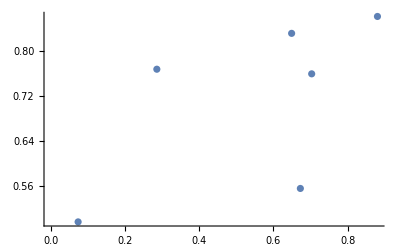

```mathematica
devs⟦All, {2,3}⟧ // ListPlot
```

```mathematica
fit = LinearModelFit[devs⟦All, {2,3}⟧,x,x]
```

FittedModel[0.547861+0.302957 x]

```mathematica
project[]
```

```mathematica
fit@1
```

0.850818

```mathematica
ns = Solve[
{ nx d +ox == x,
 ny d + oy == y}, {nx, ny}]
```

(nx→(-ox+x)/d | ny→(-oy+y)/d)

```mathematica
mag =√(nx^2+ny^2)/.ns ⟦1⟧
```

√((-ox+x)^2/d^2+(-oy+y)^2/d^2)

```mathematica
Simplify@Assuming[ d>0,({nx,ny}/.ns⟦1⟧)/mag ]
```

{(-ox+x)/(d √(((ox-x)^2+(oy-y)^2)/d^2)),(-oy+y)/(d √(((ox-x)^2+(oy-y)^2)/d^2))}

```mathematica
?Assuming
```

Assuming[assum,expr] evaluates expr with assum appended to $Assumptions, so that assum is included in the default assumptions used by functions such as Refine, Simplify, and Integrate.

```mathematica
{(-ox+x)/(√((ox-x)^2+(oy-y)^2)),(-oy+y)/(√((ox-x)^2+(oy-y)^2))} /. y-> (x a + b) //Simplify
```

{(-ox+x)/(√((ox-x)^2+(b-oy+a x)^2)),(b-oy+a x)/(√((ox-x)^2+(b-oy+a x)^2))}

```mathematica
StringReplace[ devs⟦All,{2,3}⟧//ToString, {"{"->"[", "}"-> "]"}]
```

[[0.672308, 0.556435], [0.702773, 0.760115], [0.879798, 0.862075], [0.648783, 0.832054], [0.286069, 0.768317], [0.0742173, 0.497004]]